Created by: ruebenko on 02-04-2020 16:30:48

### Categorization

Tutorial

Applications

Applications`

FEMAddOns/tutorial/ViscousHeatEquation

Synonyms

### Keywords

Viscous

Viscous heat

Viscous heat equation

heat propagation

heat conduction

Second sound

Fourier's law

crystal

Details

# Steady-state solution of the viscous heat equations

Michele Simoncelli, Nicola Marzari, and Andrea Cepellotti

In this notebook we use the finite-element method to solve the viscous heat equations,  two differential equations for heat conduction in crystals that generalize Fourier's law and explain why heat propagation can become fluid like, rather than diffusive, in electronic or phononic devices. A theoretical derivation of these equations can be found in Ref. [1].

Load the FEM package.

```mathematica
Needs["NDSolve`FEM`"]
```

### Domain and mesh setup

Definition of the 2D domain, which corresponds to the in-plane (x,y) section of a 3D domain infinite in the z direction. Dimensions are in micrometer,  see [1] for details.

Set up geometric parameters.

```mathematica
yjumpum=3.0;
xjumpum=3.0;
lengthBoxum=15.0;
widthBoxum=9.0;
```

Set up smoothing radius.

```mathematica
radius=0.15;
```

Create a region and a mesh from the region.

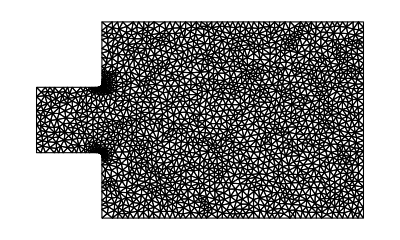

```mathematica
MainShape=ImplicitRegion[((0.0≤x≤lengthBoxum)&&(0.0≤y≤ widthBoxum)) &&                           (!(((0.0≤ x< xjumpum)&&(0.0≤ y<yjumpum)) ||((0.0≤ x< xjumpum)&&((widthBoxum-yjumpum)< y≤ widthBoxum))))  ,{x,y}];
HighDisk=Disk[{xjumpum-radius,widthBoxum-yjumpum+radius},radius,{3/2*Pi,2*Pi}];
HighRect=ImplicitRegion[(xjumpum-radius≤ x≤ xjumpum) &&((widthBoxum-yjumpum)≤y≤ (widthBoxum-yjumpum+radius)),{x,y}];
ToAddHigh=RegionDifference[HighRect,HighDisk];
LowDisk=Disk[{xjumpum-radius,yjumpum-radius},radius,{0,Pi/2}];
LowRect=ImplicitRegion[(xjumpum-radius≤ x≤ xjumpum) &&((yjumpum-radius)≤y≤ (yjumpum)),{x,y}];
ToAddLow=RegionDifference[LowRect,LowDisk];
Ω=RegionUnion[ MainShape,ToAddLow,ToAddHigh];
emesh=ToElementMesh[Ω,"MaxCellMeasure"->{"Length"->lengthBoxum/30.0},AccuracyGoal-> 5,MeshQualityGoal->1]; 
emesh["Wireframe"]
```

### Parameters entering into the viscous heat equations

We are assuming that the sample is made of polycrystalline graphite with a grain size equal to 10 μm. Under these conditions, Ref. [1] gives the following numerical values for the parameters entering into the viscous heat equations:

Set up material parameters.

```mathematica
Subscript[μ, a]=    0.000907647; (*in picog/(micrometer*ns), this accounts for a grain size equal to 10 μm*)
Subscript[μ, b]=    0.000485155; (*in picog/(micrometer*ns), this accounts for a grain size equal to 10 μm*)
Subscript[μ, c]=    0.000401477; (*in picog/(micrometer*ns), this accounts for a grain size equal to 10 μm*) 
W=      3.252493000; (*in micrometer/ns*) 
Subscript[C, V]= 0.000184524;  (*Specific heat, in picog/(micrometer*ns^2*K)*) 
A=      0.000320256; (*Specific momentum, in pg/micrometer^3*)
Subscript[D, u]= 0.979531000;   (*Umklapp momentum dissipation timenscale, in ns^-1, this accounts for a grain size equal to 10 μm*)
κ=      0.002721340; (*Thermal conductivity, in picog*micrometer/(K*ns^3), this accounts for a grain size equal to 10 μm*)
Subscript[T, eq]=70.000000000; (*Equilibrium temperature around which a temperature perturbation is applied, in K *)
δT=10.0 (*temperature perturbation, in K *);
```

### Equations setup

The viscous heat equations are given by Eq. (10) and Eq. (11) of Ref. [1]. Here we consider the steady-state  and a sample infinite in the z direction, therefore the equations that we have to solve assume the following form:

Set up the viscous heat equation.

```mathematica
EqUx=Derivative[1,0][T][x,y]*W*√((Subscript[C, V]*A)/Subscript[T, eq])-Subscript[μ, a]*Derivative[2,0][Ux][x,y]-Subscript[μ, b]*Derivative[0,2][Ux][x,y]-Subscript[μ, c]*Derivative[1,1][Uy][x,y]+(Subscript[D, u]*A)*Ux[x,y] ;
EqUy=Derivative[0,1][T][x,y]*W*√((Subscript[C, V]*A)/Subscript[T, eq])-Subscript[μ, b]*Derivative[2,0][Uy][x,y]-Subscript[μ, a]*Derivative[0,2][Uy][x,y]-Subscript[μ, c]*Derivative[1,1][Ux][x,y]+(Subscript[D, u]*A)*Uy[x,y] ;
EqT=(W*√(Subscript[T, eq]*A*Subscript[C, V]))* (Derivative[1,0][Ux][x,y]+Derivative[0,1][Uy][x,y])-κ *Derivative[2,0][T][x,y] -κ *Derivative[0,2][T][x,y];
Operator={EqUx,EqUy,EqT};
```

We use no-slip condition for the drift velocity (Ux=0 and Uy=0 at all the boundaries). For the temperature T(x=0μm)=80 K, T(x=15μm)=60 K are set.

Set up Dirichlet boundary conditions.

```mathematica
bcs={DirichletCondition[{Ux[x,y]==0.,Uy[x,y]==0.},True],
DirichletCondition[T[x,y]==Subscript[T, eq]-δT,(x==lengthBoxum) && (0.0≤ y≤ widthBoxum)],
DirichletCondition[T[x,y]==Subscript[T, eq]+δT,(x==0.0) && (yjumpum≤ y≤ (widthBoxum-yjumpum))]
};
```

All the boundaries with x≠0 or x≠15 μm are adiabatic which is modeled with a Neumann zero boundary condition. Since the Neumann zero boundary condition is the default condition nothing needs to be specified.

Set up the PDE.

```mathematica
pde = Operator == {0,0,0};
```

### Equations solving

To solve the equations NDSolve is used. NDSolve needs some help to figure out what the dependent variable ordering is. This is specified with the option DependentVariables. More information on the dependent variable ordering can be found in the documentation section Ordering of Dependent Variable Names.

Solve the equations.

```mathematica
{Ux0,Uy0,T0}=NDSolveValue[{pde,bcs},{Ux,Uy,T},{x,y}∈emesh,DependentVariables->{Ux,Uy,T}];
```

### Analysis of the viscous heat equations’ solution

Plot of the temperature profile obtained from the solution of the viscous heat equations.

Plot the temperature profile.

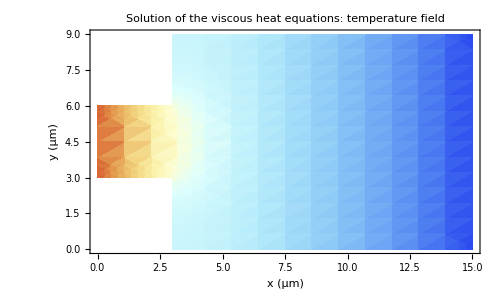

```mathematica
DensityPlot[T0[x,y],{x,0,lengthBoxum},{y,0,widthBoxum},
ColorFunction->"LightTemperatureMap",
PlotLegends->BarLegend[Automatic,LegendLabel->Placed["Temperature (K)",Below]],
AspectRatio->widthBoxum/lengthBoxum,
ImageSize->{500,300},
Axes-> True,
AxesOrigin->{0,0},
PlotRange->{{0,lengthBoxum},{0,widthBoxum}},
FrameLabel->{"x (μm)","y (μm)"},
LabelStyle->Directive[12,Black,Plain], 
PlotLabel->"Solution of the viscous heat equations: temperature field"]
```

Plot the drift-velocity profile resulting from the solution of the viscous heat equations.

Plot the velocity profile.

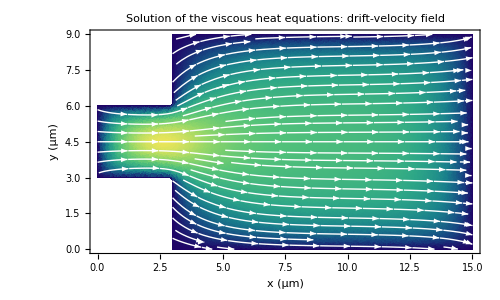

```mathematica
StreamDensityPlot[{{Ux0[x,y],Uy0[x,y]},((Ux0[x,y])^2+(Uy0[x,y])^2)^0.5 },{x,y}∈ Ω,
StreamPoints->Fine,
StreamStyle->White,
PlotLegends->BarLegend[Automatic,LegendLabel->Placed["drift velocity module (μm/ns)",Below]],
ColorFunction->ColorData["BlueGreenYellow"],
AspectRatio->widthBoxum/lengthBoxum, ImageSize->{500,300},
Frame->True,
FrameLabel->{"x (μm)","y (μm)"},
Axes-> True,
AxesOrigin->{0,0},
PlotRange->{{0,lengthBoxum},{0,widthBoxum}},
LabelStyle->Directive[12,Black,Plain],
FrameStyle->Black,
PlotLabel->"Solution of the viscous heat equations: drift-velocity field"]
```

### References

[1] M. Simoncelli, N. Marzari, and A. Cepellotti, Phys. Rev. X 10, 011019 (2020), https://link.aps.org/doi/10.1103/PhysRevX.10.011019

More About

Related Tutorials

Related Wolfram Training Courses